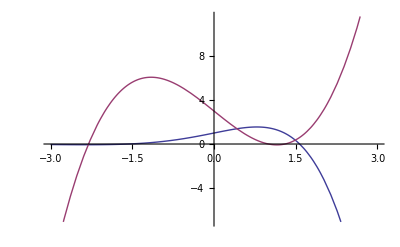

```mathematica
(* graphics within mathematica *)

(* 1. superposition of two simple plots specified in a list of expressions*)

plot1=Plot[{Exp[x] Cos[x],x^3-4x+3},{x,-3,3}]
```

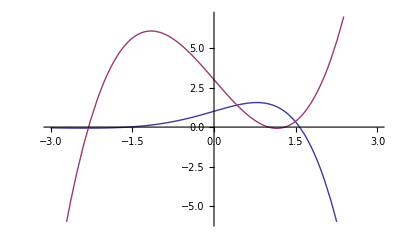

```mathematica
(* 2. If we want to specify the verical range, we can say: *)
plot2=Plot[{Exp[x] Cos[x],x^3-4x+3},{x,-3,3}, PlotRange->{-6,7}]
```

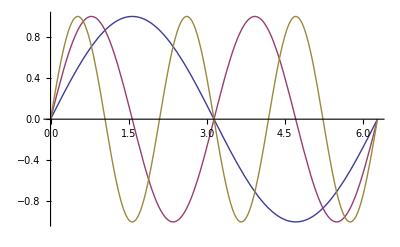

```mathematica
(* 3. You can specify a LIST OF EXPRESSIONS using the Table command, as well, not just like in the preceeding example *)
(* Do not forget to write the Evaluate inside the plotting command; when you use a COMMAND (like Table for example) inside a plotting routine, you must use Evaluate to force the evaluation of the command *)
Plot[Evaluate[Table[Sin[c*x],{c,1,3}]],{x,0,2Pi}]
```

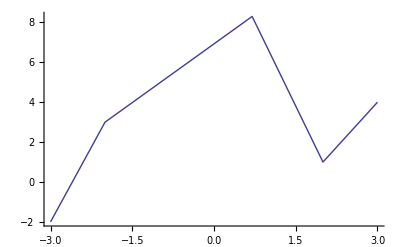

```mathematica
plot3=ListPlot[{{-3,-2},{-2,3},{0.7,8.3},{2,1},{3,4}},Joined->True]
```

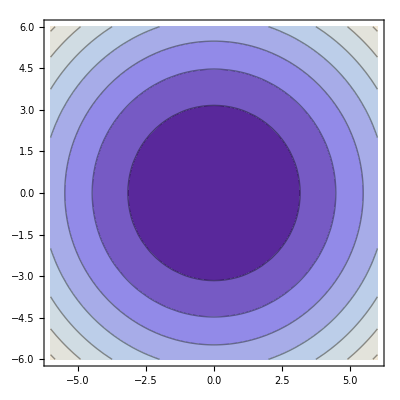

```mathematica
(* 4. Contourplot *)
plot4=ContourPlot[x^2+y^2,{x,-6,6},{y,-6,6}] (* ContourShading->False turns off the shading, Contours-> n can give n contours,
Contours-> {a,b,...} would produce contours at the levels a,b,..*)
```

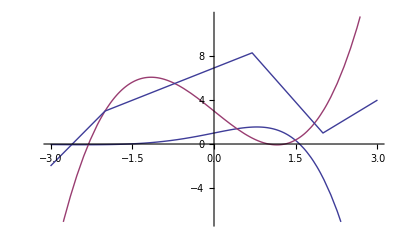

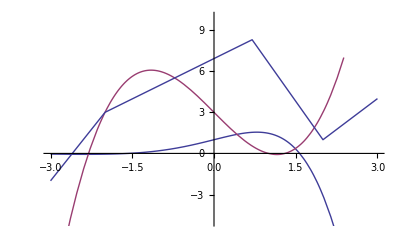

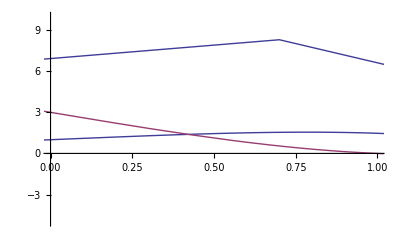

```mathematica
(* 5. Superposition of existing plots : Show command *)
Show[plot1,plot3] (* Of course, there are a lot of additional commands you can use to control the superposition: *)
Show[plot2,plot3,PlotRange->{-5,10}]  (* We only specified the vertical range here *)
Show[plot2,plot3,PlotRange->{{0,1},{-5,10}}] (* Here both x and y range are specified *)
```

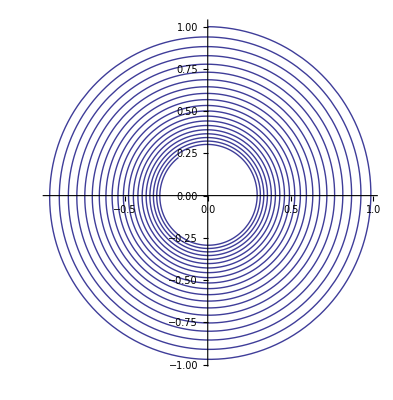

```mathematica
(* 6. Parametric plots {f[t],g[t], t in interval *)
ParametricPlot[{Exp[-t/100] Sin[t],Exp[-t/100]  Cos[t]},{t,0,125},AspectRatio->Automatic] (* Automatic uses now the same axis scale for both axes; default is the Golden ratio *)
```

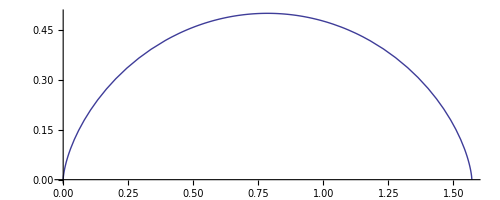

-Graphics-

```mathematica
(* Another example of a parametric plot by using Evaluate *)
f[t_]:={(t-Sin[t])/4,(1-Cos[t])/4};
ParametricPlot[f[t],{t,0,2Pi}]
(* Equivalent is : *) ParametricPlot[Evaluate[f[t]],{t,0,2Pi}]
```

```mathematica
(* 7. 3D plots *)
Plot3D[x^2-x*y^2,{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(* 8. 3D parametric plots *)
ParametricPlot3D[{(2+Cos[t])*Cos[u],(2+Cos[t])*Sin[u],Sin[t]},{t,0,2Pi},{u,0,2Pi}] (* Torus ; you try to produce  a sphere with a radius of one*)
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],t/4},{t,0,2Pi}] (* Helix *)
```

-Graphics3D-

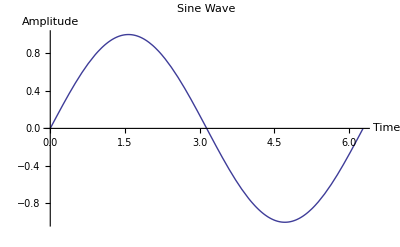

```mathematica
(* 9. Labeling and other fine details*)
Plot[Sin[t],{t,0,2Pi},AxesLabel->{"Time","Amplitude"},PlotLabel->"Sine Wave"]
```

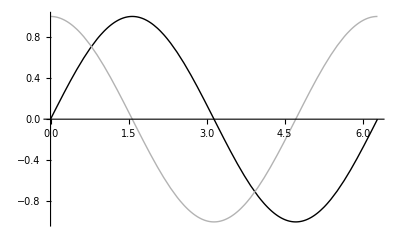

```mathematica
(* 9.1. Use PlotStyle option for controlling the grey level (0 for black, 1 for white)or color using RGB color for specifying reg, green and blue components for a color plot*)
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->{GrayLevel[0],GrayLevel[0.7]}]
```

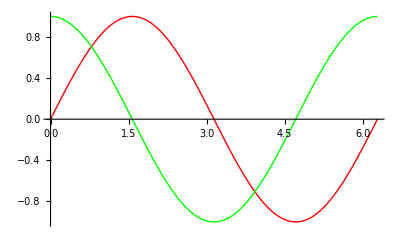

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
```

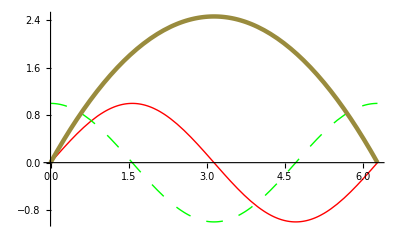

```mathematica
(* 9.2. Again use PlotStyle for other purpose and use more than one option for each curve *)
Plot[{Sin[x],Cos[x],x*(2Pi-x)/4},{x,0,2Pi},PlotStyle->{{RGBColor[1,0,0]},{Dashing[{0.03}],RGBColor[0,1,0]},Thickness[0.008]}]
```

```mathematica
(* 10. Animation *)
Manipulate[Plot[Cos[n*x],{x,0,2Pi},PlotRange->{-1,1}],{n,1,5,0.2}]
```

```mathematica
Manipulate[Plot[{x^2,1+(x-1)*(2+h)},{x,0,2},PlotRange->{-2,4},AspectRatio->Automatic],{h,0.95,0.05,-0.05}] 
(* Tangent at x=1 is y=2(x-1)+1. Examine behaviour for values of slope around 2 *)
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2Pi}],{n,1,10}]
```

```mathematica
Manipulate[Expand[(1+x)^n],{n,0,100,1}]  (*Role of manipulate*)
```